## PROTON TO ROPER TFF DATA 15/03/2017

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Mo16data:=ErrorListPlot[{{{0.649999976,0.0674641803},ErrorBar[0.01751679]},{{0.949999988,0.0762328506},ErrorBar[0.0176014826]},{{1.29999995,0.095839642},ErrorBar[0.019425964]}},PlotStyle->{Directive[Darker[Black,0.4]],PointSize[10],AbsoluteThickness[2]}]

Mo12data:=ErrorListPlot[{{{0.316885,0.0543},ErrorBar[0.01226]},{{0.373472,0.0587},ErrorBar[0.00914]},{{0.430059,0.0592},ErrorBar[0.01055]},{{0.486646,0.0642},ErrorBar[0.00798]},{{0.543232,0.0789},ErrorBar[0.01248]},{{0.599819,0.0641},ErrorBar[0.00857]},{{0.656406,0.0562},ErrorBar[0.01549]}},
PlotStyle->{Directive[Darker[Green,0.4]],PointSize[10],AbsoluteThickness[2]}]

Az09data:=ErrorListPlot[{{{0.325211,0.0554529},ErrorBar[0.006793]},{{0.437557,0.0579482},ErrorBar[0.0069316]},{{0.549902,0.0718115},ErrorBar[0.0090111]},{{0.715464,0.0754159},ErrorBar[0.0106747]},{{0.999285,0.0903882},ErrorBar[0.0133088]},{{1.93352,0.107024},ErrorBar[0.0134472]},{{2.30604,0.0945471},ErrorBar[0.0130316]},{{2.74951,0.0679298},ErrorBar[0.0099815]},{{3.28758,0.0585028},ErrorBar[0.007902]},{{3.92618,0.0451941},ErrorBar[0.0102588]},{{4.69486,0.0418669},ErrorBar[0.0112293]}},PlotStyle->{Directive[Darker[Red,0.4]],PointSize[10],AbsoluteThickness[2]}]
```

```mathematica
gTFF1data6:=Show[Mo12data,Az09data,Mo16data,PlotRange->{{0,6},{0,0.15}},AspectRatio->0.8,FrameLabel->{"Q^2(GeV^2)","F_(1N→N^*)^p(Q^2)"},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->14}]
```

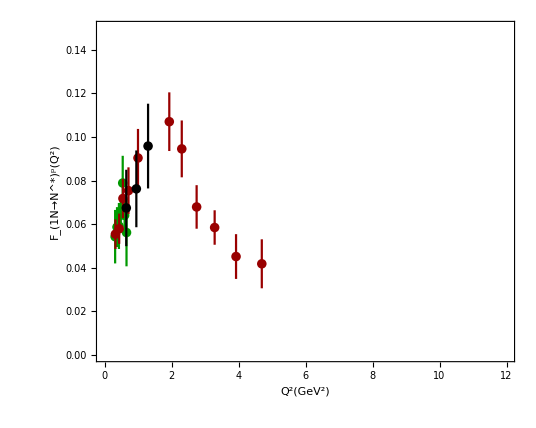

```mathematica
gTFF1data12=Show[Mo12data,Az09data,Mo16data,PlotRange->{{0,12},{0,0.15}},AspectRatio->0.8,FrameLabel->{"Q^2(GeV^2)","F_(1N→N^*)^p(Q^2)"},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->14}]
```

```mathematica
gTFF2dataa:=ErrorListPlot[{{{0.649999976,0.0438743494},ErrorBar[0.0113917897]},{{0.949999988,0.057172969},ErrorBar[0.0132007264]},{{1.29999995,0.0731263086},ErrorBar[0.0148221441]}},PlotStyle->{Directive[Darker[Black,0.4]],AbsolutePointSize[8],AbsoluteThickness[2]}]

gTFF2datab:=ErrorListPlot[{{{0.316885,-0.300654},ErrorBar[0.110455]},
{{0.373472,-0.198215},ErrorBar[0.0479896]},
{{0.430059,-0.127115},ErrorBar[0.0359157]},
{{0.486646,-0.11701},ErrorBar[0.03102]},
{{0.543232,-0.05758},ErrorBar[0.033725]},
{{0.599819,0.02424},ErrorBar[0.047121]},
{{0.656406,0.03698},ErrorBar[0.053184]}},PlotStyle->{Directive[Darker[Green,0.6]],AbsolutePointSize[10],AbsoluteThickness[2]}]

gTFF2datac:=ErrorListPlot[{{{0.333206,-0.1875},ErrorBar[0.030556]},
{{0.444276,-0.1472},ErrorBar[0.032639]},
{{0.561191,-0.0541},ErrorBar[0.042361]},
{{0.730716,-0.0097},ErrorBar[0.035416]},
{{1.011310, 0.0263},ErrorBar[0.036111]},
{{1.94079, 0.1222},ErrorBar[0.024305]},
{{2.3149, 0.125},ErrorBar[0.017361]},
{{2.75919, 0.091},ErrorBar[0.0125]},
{{3.29699, 0.05416},ErrorBar[0.0125]},
{{3.92833, 0.03472},ErrorBar[0.01041]},
{{4.69997, 0.00833},ErrorBar[0.01111]}},PlotStyle->{Directive[Darker[Red,0.4]],AbsolutePointSize[10],AbsoluteThickness[2]}]
```

```mathematica
gTFF2data6:=Show[gTFF2dataa,gTFF2datab,gTFF2datac,PlotRange->{{0,6},{-0.43,0.25}},AspectRatio->0.8,FrameLabel->{"Q^2(GeV^2)","F_(2N→N^*)^p(Q^2)"},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->12}]
```

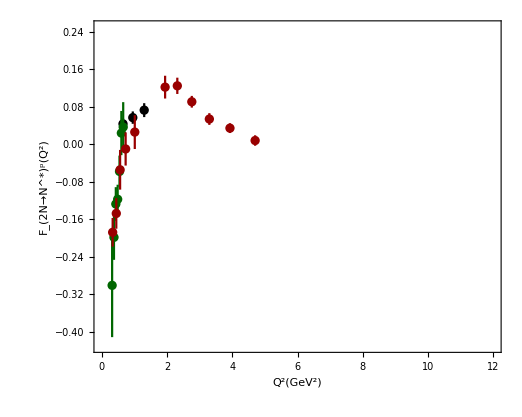

```mathematica
gTFF2data12=Show[gTFF2dataa,gTFF2datab,gTFF2datac,PlotRange->{{0,12},{-0.43,0.25}},AspectRatio->0.8,FrameLabel->{"Q^2(GeV^2)","F_(2N→N^*)^p(Q^2)"},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->12}]
```